# Calculating stuff for Kagome lattice

## First look at 3-site tight-binding model

This has exact solution, see Appendix A of the paper “Fermionization of bosons in a flat band” by Saurabh Maiti and Tigran Sedrakyan.

We want to find eigenvalues of the Hamiltonian 

  H_k  =  J_1 (0 | H_2 | H_1
H_2 | 0 | H_3
H_1 | H_3 | 0) 

where   J_1   is the nearest-neighbor hopping matrix element, and   H_i  =  (e^(ⅈ k.a_i /2) + e^(-ⅈ k.a_i /2)) ,   and the vectors   a_i are given by   

a_1 = a(1
0)

a_2 = a(1/2
√3/2)

a_3 = a(1/2
-√3/2)

```mathematica
ClearAll["Global'*"]
Clear[a1,a2,a3,a,H,Ham,kx,ky, G1, G2]

a1 = {1,0};
a2 = {1/2, √3/2};
a3 = {1/2, -√3/2};
a = {a1,a2,a3};

H[ind_, kx_, ky_] := Exp[ⅈ {kx,ky}.a⟦ind⟧/2] + Exp[-ⅈ {kx,ky}.a⟦ind⟧/2];

Ham[kx_,ky_] = -{{0, H[2,kx,ky], H[1,kx,ky]},{H[2,kx,ky],0,H[3,kx,ky]},{H[1,kx,ky],H[3,kx,ky],0}};

Plot3D[Sort@Eigenvalues[Ham[kx,ky]], {kx,-8,8},{ky,-8,8}, ImageSize->Large, PlotPoints->50]
```

-Graphics3D-

## Real space and k-space potentials

I plot the kagome lattice in real space, then plot the fourier transform of the lattice potential. Since the fourier transform is a bunch of delta functions, I replace this with exp(-r^2) for plotting purposes.

The fourier transform is just what you get from transforming the 6 cosine terms in the potential, each term creates a +/-k coupling in k-space. For kagome this means +1 weight on 1064 terms, -0.5 on the 532 terms. 

I add the scaleK variable as a hack to get around a dumb property of the FourierTransform function. If you run the following:

FourierTransform[Cos[4x],x,k]
FourierTransform[Cos[2x],x,k]
FourierTransform[Cos[1x],x,k]
FourierTransform[Cos[1/2x],x,k]
FourierTransform[Cos[1/4x],x,k]

You would see that the coefficient in front of the DiracDeltas is independent of k for k>1, but depends on k for k<1.... Doesn’t make any sense.

```mathematica
eval = {AF->2, AH -> -1, ϕ1-> 0, ϕ2->0};
scaleK = 10;

G1 = {Sin[π/6],Cos[π/6]};
G2 = {Sin[-π/2], Cos[-π/2]};

V[x_,y_] = (AF(Cos[scaleK G1.{x,y}] + Cos[scaleK G2.{x,y}] + Cos[-scaleK (G1+G2).{x,y}]) + AH(Cos[2 scaleK G1.{x,y}+ϕ1] + Cos[2 scaleK G2.{x,y}+ϕ2] + Cos[-2scaleK (G1+G2).{x,y}]))/.eval;

fourierKagome[kX_,kY_]=FourierTransform[V[x,y],{x,y},{kX, kY}]/.DiracDelta[a_]:> Exp[-Abs[a]^2/1^2]/.DiracDelta[c_,d_]:> Exp[-Abs[c-d]^2/1^2];

DensityPlot[V[x/scaleK,y/scaleK],{x,-10,10},{y,-10,10}, ColorFunction->"IslandColors", PlotRange->All, PlotPoints->100, PlotLabel->Style["Real space kagome potential",FontSize->20]]

Quiet@DensityPlot[fourierKagome[kX scaleK,kY scaleK], {kX, -3, 3},{kY,-3,3}, PlotPoints->200, ColorFunction->"SunsetColors", PlotRange->All, PlotLegends->{BarLegend["SunsetColors"]}, PlotLabel->Style["k-space kagome potential",FontSize->20]]
```

-Graphics-

-Graphics-

## Including more momentum states

Below I create a triangular lattice in momentum space and solve for the eigenvalues. By including more basis vectors you can solve for more energy levels. The FFT of the Kagome potential is just a honeycomb in momentum space, with +1 weight on the nearest neighbor couplings and -0.5 on the next nearest neighbors. So this is what I use for the couplings between momentum states. 

The square lattice below is indexed such that rows correspond to constant k_y (horizontal in (k_x,k_y) ). Every other row is shifted by k_x→ k_x + 0.5  to account for the triangular lattice shifts between planes. Please don’t read the KagomeCoupling code... I don’t know what else to do besides brute force it... But you can trust it’s right because you get the flat bands you’d expect ;P

```mathematica
Clear[matDim];
ClearAll["Global`*"];

KagomeCoupling[dim_] := Module[{matDim = dim},
	(*Initialize matrix*)
	matTemp = ConstantArray[0,{matDim^2,matDim^2}];

	(*Loop over rows*)
	For[k=1,k≤ matDim^2,k++,
		(*set the stagger variable to account for hexagonal NN shifts.*)
		stag = Mod[Mod[Floor[(k-1)/matDim],2] + Mod[Floor[(matDim-1)/2],2],2];
		
		(*Left boundary*)
		If[Mod[k,matDim]==1, 
			(*Neighbors to the right*)
			matTemp⟦k,k+1⟧ = 1;
			matTemp⟦k,k+2⟧ = -0.5;

			(*Neighbor(s) below*)
			If[k+matDim≤matDim^2,
				matTemp⟦k,k+matDim⟧ = 1;
				If[stag> 0,
					matTemp⟦k,k+matDim+1⟧ = 1;
				];
				If[k+2matDim ≤ matDim^2,
					matTemp⟦k,k+2matDim+1⟧ = -0.5;
				];
			];

			(*Neighbor(s) above*)
			If[k-matDim>0,
				matTemp⟦k,k-matDim⟧ = 1;
				If[stag> 0,
					matTemp⟦k,k-(matDim-1)⟧ = 1;
				];
				If[k-2matDim>0,
					matTemp⟦k,k-(2matDim-1)⟧ = -0.5;
				];
			];
		];


		(*Right boundary*)
		If[Mod[k,matDim]==0, 
			(*Neighbor to the left*)
			matTemp⟦k,k-1⟧ = 1;
			matTemp⟦k,k-2⟧ = -0.5;

			(*Neighbor(s) below*)
			If[k+matDim≤matDim^2,
				matTemp⟦k,k+matDim⟧ = 1;
				If[stag== 0,
					matTemp⟦k,k+matDim-1⟧ = 1;
				];
				If[k+2matDim ≤ matDim^2,
					matTemp⟦k,k+2matDim-1⟧ = -0.5;
				];
			];
			
			(*Neighbor(s) above*)
			If[k-matDim>0,
				matTemp⟦k,k-matDim⟧ = 1;
				If[stag==0,
					matTemp⟦k,k-(matDim+1)⟧ = 1;
				];
				If[k-2matDim>0,
					matTemp⟦k,k-(2matDim+1)⟧ = -0.5;
				];
			];
		];

		(*Do the center columns*)
		If[Mod[k,matDim]>1 && Mod[k,matDim]<matDim,
			(*Left and right neighbors*)
			matTemp⟦k,k-1⟧ = 1;
			matTemp⟦k,k+1⟧ = 1;

			(*Left and right next nearest neighbor*)
			If[Mod[k,matDim]>2,
				matTemp⟦k,k-2⟧ = -0.5;
			];
			If[Mod[k,matDim]<matDim-1,
				matTemp⟦k,k+2⟧ = -0.5;
			];

			(*Neighbors above*)
			If[k-matDim>0,
				matTemp⟦k,k-matDim⟧ = 1;
				If[stag==0,
					matTemp⟦k,k-(matDim+1)⟧ = 1;
				,
					matTemp⟦k,k-(matDim-1)⟧ = 1;
				];
				If[k-2matDim>0,
					matTemp⟦k,k-(2matDim+1)⟧ = -0.5;
					matTemp⟦k,k-(2matDim-1)⟧ = -0.5;
				];
			];

			(*Neighbors below*)
			If[k+matDim<matDim^2,
				matTemp⟦k,k+matDim⟧ = 1;
				If[stag==0,
					matTemp⟦k,k+(matDim-1)⟧ = 1;
				,
					matTemp⟦k,k+(matDim+1)⟧ = 1;
				];
				If[k+2matDim ≤ matDim^2,
					matTemp⟦k,k+2matDim-1⟧ = -0.5;
					matTemp⟦k,k+2matDim+1⟧ = -0.5;
				];
			];		
		];
	];
	matTemp
];

KagomeKE[dimension_,kX_,kY_, F_:0,θ_:0,time_:t] := Module[{matDim = dimension},
	(*Initialize matrix*)
	matTemp = ConstantArray[0,{matDim^2,matDim^2}];
	
	(* Loop over the diagonal of the matrix *)
	For[k=1,k≤ matDim^2,k++,
		(*Check the stagger of the row*)
		stag = Mod[Mod[Floor[(k-1)/matDim],2] + Mod[Floor[(matDim-1)/2],2],2];
		(*Update ky which doesn't depend on stagger*)
		ky = (√3)/2((matDim-1)/2-Floor[(k-1)/matDim]) + F t Sin[θ];
		(*Update kx*)
		If[stag==0,
			kx = Mod[k-1,matDim]-(matDim-1)/2 + F t Cos[θ];
		,
			kx = 0.5+Mod[k-1,matDim]-(matDim-1)/2;
		];

		(*Put k^2 in the diagonal*)
		matTemp⟦k,k⟧ = ((kx+kX)^2+(ky+kY)^2);
	];
	matTemp
];
```

Create the Hamiltonian and solve for the eigenvalues at some k-point. Not that the time to compute things scales very strongly with dimKagome: the matrix dimension scales like dimKagome^2, then if other algorithms (like finding eigenvalues) scale with a higher power of dimensionality then you get slow computations.

```mathematica
Clear[HamKagome, Diags, OffDiags]

(*create matrix that is (dimKagome^2) x (dimKagome^2) *)
dimKagome = 13;  

OffDiags = KagomeCoupling[dimKagome];
Diags[kX_,kY_] = KagomeKE[dimKagome,kX,kY];
HamKagome[kX_,kY_,U_] = Diags[kX,kY] + U *OffDiags;

MatrixForm@OffDiags;
MatrixForm@Diags[kX,kY];
MatrixForm@HamKagome[kX,kY,U];

Print["The output below is in the format {time to solve, sorted eigenvalues}"]
RepeatedTiming@Sort[N@Eigenvalues@HamKagome[1,1,1], Less]
```

The output below is in the format {time to solve, sorted eigenvalues}

{0.0041,{-1.99253,-1.90097,-1.71133,-0.367064,-0.0594881,0.750007,1.15893,1.34712,1.56449,2.11035,2.68336,3.16081,3.53742,3.61285,3.89513,3.99426,4.1926,4.82239,4.8807,5.5479,5.70984,6.13893,6.44042,6.47143,6.99067,7.10219,7.38493,7.51321,7.60925,8.04416,8.27506,8.30222,8.77428,9.35723,9.77365,9.96826,10.0318,10.6882,10.7049,10.7112,10.7622,11.5795,11.8895,11.9793,12.165,12.7338,12.7479,13.3018,13.317,13.6818,13.9606,13.9831,14.3343,14.3531,15.4138,15.6998,15.7103,15.7689,16.2942,16.8182,16.829,16.9391,16.9611,17.5531,17.5767,17.7619,17.7902,18.5227,18.9351,19.4905,19.5158,19.7036,20.5344,20.5979,20.6662,20.7576,21.0688,21.6537,21.9172,22.0005,22.0842,22.1962,23.1808,23.2731,23.9014,23.9446,24.1338,24.2206,24.3154,24.4177,25.5258,25.5706,25.7993,26.2578,26.3357,26.7794,27.0172,27.0929,27.0965,29.1264,29.1288,29.3787,29.5578,30.0369,30.4523,30.836,31.0138,31.1749,31.636,31.988,32.429,33.1169,33.5134,34.013,34.152,34.1664,34.2168,34.8551,34.8745,36.165,36.175,36.7188,37.009,37.2096,39.6089,40.0107,40.3345,40.8366,40.8562,41.6255,42.4119,42.5432,42.7412,42.8426,42.8486,43.258,44.0154,44.7977,45.0443,45.2198,46.0393,47.7056,47.7089,48.8595,48.9886,49.7272,50.231,52.0736,53.7605,54.4578,54.6948,54.7113,55.4765,56.2632,56.6989,57.0038,58.9187,59.2998,60.2567,63.6007,63.7084,66.022,67.6468,68.2711,70.1399,71.0492,74.7566,84.4515,87.9082}}

Below plots the band structure, and it takes a while to run (~a few minutes for dimKagome = 13). Currently I solve for all eigenvalues when we only plot the lowest. So if we could solve for the six lowest energy states directly that would be speed this up, but when I used Eigenvalues[Ham,6] it didn’t return the lowest 6 as sorted by eigenvalue, so that didn’t seem to work.

```mathematica
kXmax = 1;
kYmax = (√3)/2;
dk = 0.02;

kPts = Table[{k1,k2},{k1,-kXmax,kXmax,dk},{k2,-kYmax,kYmax,dk}];

eigs = Transpose@MapThread[Sort[N@Eigenvalues[HamKagome[#1,#2,2]],Less] &,Transpose@Flatten[kPts,1]];

bands = Transpose[{Transpose[Flatten[kPts,1]]⟦1⟧,Transpose[Flatten[kPts,1]]⟦2⟧,eigs⟦#⟧}]&/@Range[9];
PlotTitles = {"Ground band","2^nd band","3^rd band","4^th band","5^th band","6^th band","7^th band","8^th band","9^th band"};
MultipleBandsTitles = {"Bands 1-3","Bands 4-6","Bands 7-9"};

Plots = ListPlot3D[bands⟦#⟧, PlotLabel->Style[PlotTitles⟦#⟧, Large]]&/@Range[9];

For[i=1,i≤ 9,i++,Print[Plots⟦i⟧]]

For[i=1,i<4,i++,
	Print@Show[Plots⟦#⟧&/@Range[3i-2,3i], PlotRange->All, ImageSize->Large, PlotLabel-> Style[MultipleBandsTitles⟦i⟧,Large]]
]

Show[Plots⟦#⟧&/@Range[9], PlotRange-> All, ImageSize->Large, PlotLabel-> Style["Bands 1-9",Large]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«9 more identical outputs»

-Graphics3D-

Now that we have the Hamiltonian working correctly, we can numerically integrate to solve for Bloch oscillations!

I added an optional force term into the Hamiltonian above. We can adiabatically load the lattice without a force, then ramp the lattice, then adiabatically unload the lattice back to free momentum states.

```mathematica
Clear[HamKagome, Diags, OffDiags]

dimKagome = 17;   (*create matrix that is (dimKagome^2) x (dimKagome^2) *)
force = 1;    (*Force during BO*)
ϕF = 0;      (*Angle of force for BO*)
n0 = (dimKagome^2+1)/2;    (*inial state at (0,0) in k-space*)
kX0 = 0;      (*Initial x momentum for atom*)
kY0 = 0;     (*initial y momentum for atom*)
LatDep = 2;   (*Lattice depth. Currently set up for Subscript[V, tot] = LatDep Subscript[V, 1064] - 1/2 LatDep Subscript[V, 532]  *)
TLoad = 4;    (*Time to adiabatically load the lattice*)
NBloch = 1;   (*Number of Bloch oscillations*)
TBloch = (4 NBloch)/force;   (*Time to Bloch oscillate*)

OffDiags = KagomeCoupling[dimKagome];
Diags[kX_,kY_, t_] = KagomeKE[dimKagome,kX,kY,force, ϕF,t];
HamKagome[kX_,kY_,U_, t_] = Diags[kX,kY,t] + U *OffDiags;
HamKagomeLoad[kX_,kY_,U_, t_] = Diags[kX,kY,0] + U (t/TLoad)*OffDiags;
HamKagomeUnload[kX_,kY_,U_, t_] = Diags[kX,kY,TBloch] + U((TLoad-t)/TLoad) *OffDiags;

MatrixForm@OffDiags;
MatrixForm@Diags[kX,kY,t];
MatrixForm@HamKagome[kX,kY,U,t];

Print["The output below is in the format {time to solve, sorted eigenvalues}"]
RepeatedTiming@Sort[N@Eigenvalues@HamKagome[1,1,1,1], Less]
```

The output below is in the format {time to solve, sorted eigenvalues}

{0.011,{-2.02955,-1.73082,-1.63343,-0.472209,0.261162,0.762333,0.948726,1.37393,1.63018,1.89159,2.48532,3.15037,3.34011,3.94112,3.99466,4.32496,4.42685,4.65618,4.73417,5.38246,5.73443,5.75364,6.14974,6.40304,6.80597,6.86308,7.25752,7.96148,8.05209,8.31923,8.53129,8.84217,9.03975,9.16319,9.45333,9.51414,10.1812,10.25,10.5164,10.7057,10.9446,11.2063,11.8159,11.8854,11.9646,12.1898,13.1721,13.4161,13.625,13.9834,13.9905,14.0738,14.9442,15.1099,15.157,15.4137,15.4551,15.7113,16.1408,16.2601,16.6481,16.9164,17.0407,17.1457,17.3564,17.7401,17.9241,18.417,18.8402,19.098,19.4375,19.5471,19.9356,20.8902,21.1293,21.2479,21.4793,21.5399,21.6618,21.816,22.4314,22.4921,22.8376,23.4422,23.5836,23.6606,23.8582,23.8895,23.9847,24.2515,24.5854,25.1439,25.486,25.7446,25.8514,26.1467,26.1964,26.7472,26.7526,26.8039,26.9896,28.1067,28.6071,28.6598,28.994,29.448,29.9283,30.1423,30.2951,30.833,30.8359,31.3564,31.3596,31.6482,31.7021,31.7428,31.8544,31.9937,32.6916,33.1994,33.2218,33.2923,33.7895,34.0087,34.0476,34.0914,34.3186,34.4319,34.6146,36.1801,36.3202,36.3673,36.466,36.9697,36.9923,37.021,37.128,37.5911,37.6105,37.9306,39.4932,39.4983,39.9036,40.1185,40.3653,40.4632,40.6351,40.7878,41.7952,41.9573,42.1915,42.4818,42.4906,42.6282,42.8769,42.9686,43.0088,43.1475,43.3283,43.9969,44.2269,44.3893,44.5379,45.1232,45.2546,45.4904,45.5442,46.0841,46.3331,46.5667,46.9846,47.2944,48.4718,48.777,49.201,49.9398,50.506,50.8368,51.2429,51.3441,52.284,52.5629,52.565,52.6644,53.5236,54.0329,54.3147,54.4056,54.6316,54.6404,55.5195,55.8286,55.9853,56.0597,56.1744,56.3714,56.6753,56.761,57.1065,58.5468,58.8417,58.9333,59.4817,60.3236,60.3649,61.4453,61.6977,62.043,63.4541,63.9396,64.0536,64.7524,64.8829,65.4318,65.9786,66.9392,67.1516,67.3238,67.8826,68.2399,68.404,68.9413,69.7929,70.0376,70.6129,70.6919,70.9576,71.3227,71.5815,72.0173,72.0637,72.1107,72.446,74.5696,74.5731,74.7074,75.4933,78.5044,79.0217,80.149,80.6605,80.6926,81.85,82.3836,82.493,83.1435,83.2318,84.3474,84.6839,85.4616,87.455,87.5115,87.8516,87.9999,88.9373,90.1543,92.2297,92.3618,92.7062,93.6311,97.0747,98.9284,98.9871,99.1312,99.6521,99.6849,100.908,101.234,101.403,101.641,102.447,103.097,106.32,106.527,107.941,111.98,115.41,116.203,118.01,118.345,119.223,120.656,122.478,126.978,135.292,138.055,140.648,143.99,162.993}}

```mathematica
ψi = ConstantArray[0,dimKagome^2];
ψi⟦n0⟧ = 1;

(*    ---- Load lattice----    *)
ψ[t_]=Table[ ci[n][t],{n,1,dimKagome^2}];
cs = Table[ ci[n],{n,1,dimKagome^2}];
ics = Table[ ci[n][0]==ψi⟦n⟧,{n,1,dimKagome^2}];
equation = ψ'[t]== -ⅈ HamKagomeLoad[kX0,kY0,LatDep,t].ψ[t];

(* Solve the main Schrodinger equation *)
soln = NDSolve[{equation,ics},cs,{t,0,TLoad}];
ψLoad[t_]=ψ[t]/.soln⟦1⟧;


(*    ---- Bloch oscillate ----    *)
Clear[ci, ψ];

ψ[t_]=Table[ ci[n][t],{n,1,dimKagome^2}];
cs = Table[ ci[n],{n,1,dimKagome^2}];
ics = Table[ ci[n][0]==ψLoad[TLoad]⟦n⟧,{n,1,dimKagome^2}];
equation = ψ'[t]== -ⅈ HamKagome[kX0,kY0,LatDep,t].ψ[t];

(* Solve the main Schrodinger equation *)
soln = NDSolve[{equation,ics},cs,{t,0,TBloch}];
ψBloch[t_]=ψ[t]/.soln⟦1⟧;


(*    ---- Unload lattice----    *)
Clear[ci, ψ];

ψ[t_]=Table[ ci[n][t],{n,1,dimKagome^2}];
cs = Table[ ci[n],{n,1,dimKagome^2}];
ics = Table[ ci[n][0]==ψBloch[TBloch]⟦n⟧,{n,1,dimKagome^2}];
equation = ψ'[t]== -ⅈ HamKagomeUnload[kX0,kY0,LatDep,t].ψ[t];

(* Solve the main Schrodinger equation for Bragg *)
soln = NDSolve[{equation,ics},cs,{t,0,TLoad}];
ψUnload[t_]=ψ[t]/.soln⟦1⟧;



(*Plot all outputs*)
loadPt = Plot[Evaluate[Hold[(Abs[ψLoad[t]]^2)⟦#⟧]&/@Range@(dimKagome^2)], {t,0,TLoad}, PlotRange->All];
boPt = Plot[Evaluate[Hold[(Abs[ψBloch[t-TLoad]]^2)⟦#⟧]&/@Range@(dimKagome^2)], {t,TLoad,TLoad+TBloch}, PlotRange->All];
unloadPt = Plot[Evaluate[Hold[(Abs[ψUnload[t-TLoad-TBloch]]^2)⟦#⟧]&/@Range@(dimKagome^2)], {t,TLoad+TBloch,2 TLoad+TBloch}, PlotRange->All];
Show[{loadPt,boPt,unloadPt},PlotRange->All]
```

-Graphics-

Now I’ll make a function to plot any state

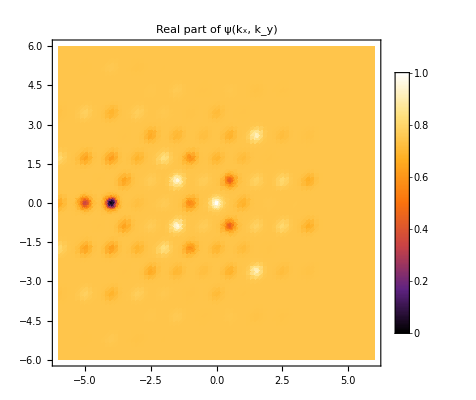

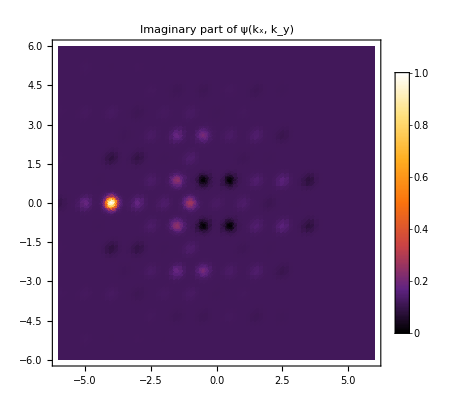

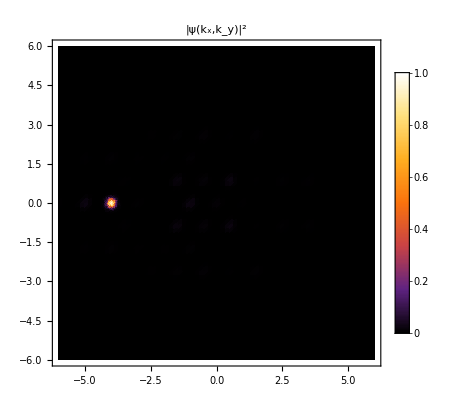

{Null,Null,Null}

```mathematica
PlotState[someψ_,reim_:False]:=Module[{ψ = someψ},
	State = 0;

	(* Loop over the elements of the state vector, add an exponential to the output *)
	For[k=1,k≤ dimKagome^2,k++,
		(*Check the stagger of the row*)
		stag = Mod[Mod[Floor[(k-1)/dimKagome],2] + Mod[Floor[(dimKagome-1)/2],2],2];
		(*Update ky which doesn't depend on stagger*)
		ky = (√3)/2((dimKagome-1)/2-Floor[(k-1)/dimKagome]);
		(*Update kx*)
		If[stag==0,
			kx = Mod[k-1,dimKagome]-(dimKagome-1)/2;
		];
		If[stag>0,
			kx = 0.5+Mod[k-1,dimKagome]-(dimKagome-1)/2;
		];

		State = State + ψ⟦k⟧Exp[-((kX-kx)^2+(kY-ky)^2)/0.2^2];
	];
	

	If[reim,
		plots = {Re[State],Im[State],Abs[State]^2};
		plotLabels = {"Real part of ψ(k_x, k_y)","Imaginary part of ψ(k_x, k_y)","|ψ(k_x,k_y)|^2"};
	,
		plots = {Abs[State]^2};
		plotLabels = {"|ψ(k_x,k_y)|^2"};
	];
	Print@Quiet@DensityPlot[plots⟦#⟧,{kX,-6,6},{kY,-6,6}, ColorFunction->"SunsetColors", PlotRange->All, PlotLabel->Style[plotLabels⟦#⟧,FontSize-> 20], PlotPoints->75, PlotLegends->BarLegend["SunsetColors"]]&/@Range[Length[plots]]
];

PlotState[ψUnload[4],True]

BlochOscillateGif = Animate[PlotState[ψBloch[t]],{t,0,4,1/4}]
```